# AOE Thin-Wall Project

Group 7 - Marika Ottman (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
gfactor=1;
grav=32.2*gfactor; (*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=117.84;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
width=.65*ctip;(*box breadth (ft)*)
height=0.05443575 ctip;(*box height (ft)*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=27.5; (*landing gear location (ft)*)
S=width*Lw; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
Wspar=ρAl*Lw*width*height;(*weight of spar (lbs)*)
e = 0.862; (* oswald effieciency factor*)

Izz=1/12 width *height^3; (*moment of inertia of lift(ft4)*)
Iyy=1/12 Lw*height^3; (*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; 
(*yield stress of wing (lb/ft2)*)
Rfuse = 10.02; (*radius of fuselage (ft)*)
```

http://asm.matweb.com/search/SpecificMaterial.asp?bassnum=ma6061t6

## Case 1 (Takeoff)

```mathematica
ClearAll["Global`*"]
```

Constants

```mathematica
gfactor=1;
grav=32.2*gfactor; (*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=117.84;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
width=.65*ctip;(*box breadth (ft)*)
height=0.05443575 ctip;(*box height (ft)*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=.105*Lw; (*landing gear location (ft)*)
S=width*Lw; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
Wspar=ρAl*Lw*width*height;(*weight of spar (lbs)*)
e = 0.862; (* oswald effieciency factor*)

Izz=1/12 width *height^3; (*moment of inertia of lift(ft4)*)
Iyy=1/12 Lw*height^3; (*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; 
(*yield stress of wing (lb/ft2)*)
Rfuse = 10.02; (*radius of fuselage (ft)*)
```

Lift

0.0577214+0.0000144596 Leng^3+(-0.0177038-0.0000433789 Leng^2) x+0.0479822 x^2-0.000394849 x^3+1.36125×10^-6 x^4+1.34229×10^-25 x^5-7.54088×10^-12 x^6

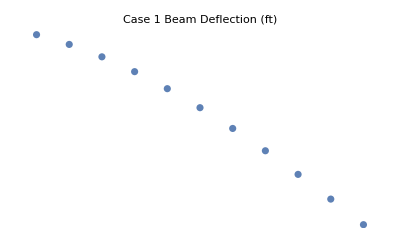

```mathematica
(* distributed load *)
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
py[x_]=a x^2+b x+c;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}](*total lift*);

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-Wspar/Lw),x]+c1a;
VyM[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c2a;
VyR[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c3a;

MzL[x_]=Integrate[-VyL[x],x]+c4a;
MzM[x_]=Integrate[-VyM[x],x]+c5a;
MzR[x_]=Integrate[-VyR[x],x]+c6a;

rotyL[x_]=Integrate[MzL[x]/(EE Izz),x]+c7a;
rotyM[x_]=Integrate[MzM[x]/(EE Izz),x]+c8a;
rotyR[x_]=Integrate[MzR[x]/(EE Izz),x]+c9a;

uyL[x_]=Integrate[rotyL[x],x]+c10a;
uyM[x_]=Integrate[rotyM[x],x]+c11a;
uyR[x_]=Integrate[rotyR[x],x]+c12a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyM[Llg];
eq9a=rotyM[Leng]==rotyR[Leng];
eq10a=uyL[Llg]==uyM[Llg];
eq11a=uyM[Leng]==uyR[Leng];
eq12a=MzL[Llg]==MzM[Llg];
eq13a=MzM[Leng]==MzR[Leng];
eq14a=VyL[Llg]+Wlg==VyM[Llg];
eq15a=VyM[Leng]+Weng==VyR[Leng];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a}];
c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyM[x_]=VyM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzM[x_]=MzM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyM[x_]=rotyM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyM[x_]=uyM[x];
uyR[x_]=uyR[x]

num=(95.8-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,95.8,num}]
data=Transpose@{Range[20,95.8,num],uvec};
ListPlot[data, PlotLabel->"Case 1 Beam Deflection (ft)", Axes-> False]
```

Drag

```mathematica
pzL[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π e AR)/Lw);
pzR[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π e AR)/Lw);
VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzR[x_]=Integrate[-pzR[x],x]+c2b;

MyL[x_]=Integrate[VzL[x],x]+c3b;
MyR[x_]=Integrate[VzR[x],x]+c4b;

rotzL[x_]=Integrate[-MyL[x]/(EE Iyy),x]+c5b;
rotzR[x_]=Integrate[-MyR[x]/(EE Iyy),x]+c6b;

uzL[x_]=Integrate[rotzL[x],x]+c7b;
uzR[x_]=Integrate[rotzR[x],x]+c8b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzR[Leng];
eq6b=uzL[Leng]==uzR[Leng];
eq7b=MyL[Leng]==MyR[Leng];
eq8b=VzL[Leng]+T==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzR[x_]=uzR[x];
```

Stress

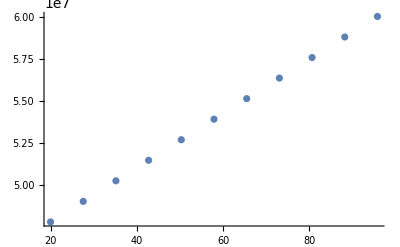

```mathematica
σxx1=-(MzL[0]*height/2)/Izz;
σxx2=(MyL[0]*-width/2)/Iyy; 
σxx=σxx1+σxx2;

num=(95.8-20)/10;
uvec={};Do[AppendTo[uvec,Abs[σxx]],{Leng,20,95.8,num}]
data=Transpose@{Range[20,95.8,num],uvec};
ListPlot[data]
```

## Case 2 (Engine Failure)

```mathematica
ClearAll["Global`*"]
```

Constants

```mathematica
gfactor=1;
grav=32.2*gfactor; (*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=117.84;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
width=.65*ctip;(*box breadth (ft)*)
height=0.05443575 ctip;(*box height (ft)*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=.105*Lw; (*landing gear location (ft)*)
S=width*Lw; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
Wspar=ρAl*Lw*width*height;(*weight of spar (lbs)*)
e = 0.862; (* oswald effieciency factor*)

Izz=1/12 width *height^3; (*moment of inertia of lift(ft4)*)
Iyy=1/12 Lw*height^3; (*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; 
(*yield stress of wing (lb/ft2)*)
Rfuse = 10.02; (*radius of fuselage (ft)*)
```

Lift

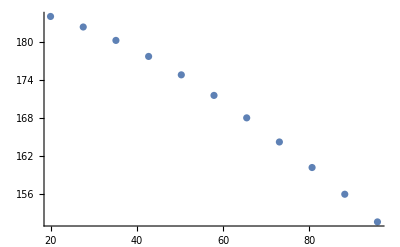

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Wto/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-Wspar/Lw),x]+c1a;
VyM[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c2a;
VyR[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c3a;

MzL[x_]=Integrate[-VyL[x],x]+c4a;
MzM[x_]=Integrate[-VyM[x],x]+c5a;
MzR[x_]=Integrate[-VyR[x],x]+c6a;

rotyL[x_]=Integrate[MzL[x]/(EE Izz),x]+c7a;
rotyM[x_]=Integrate[MzM[x]/(EE Izz),x]+c8a;
rotyR[x_]=Integrate[MzR[x]/(EE Izz),x]+c9a;

uyL[x_]=Integrate[rotyL[x],x]+c10a;
uyM[x_]=Integrate[rotyM[x],x]+c11a;
uyR[x_]=Integrate[rotyR[x],x]+c12a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyM[Llg];
eq9a=rotyM[Leng]==rotyR[Leng];
eq10a=uyL[Llg]==uyM[Llg];
eq11a=uyM[Leng]==uyR[Leng];
eq12a=MzL[Llg]==MzM[Llg];
eq13a=MzM[Leng]==MzR[Leng];
eq14a=VyL[Llg]+Wlg==VyM[Llg];
eq15a=VyM[Leng]+Weng==VyR[Leng];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a}];
c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyM[x_]=VyM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzM[x_]=MzM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyM[x_]=rotyM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyM[x_]=uyM[x];
uyR[x_]=uyR[x];

num=(95.8-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Lw]],{Leng,20,95.8,num}]
data=Transpose@{Range[20,95.8,num],uvec};
ListPlot[data]
```

Drag

```mathematica
pzL[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π e AR)/Lw);
pzR[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π e AR)/Lw);

VzL[x_]=Integrate[-pzL[x],x]+c1b;
VzR[x_]=Integrate[-pzR[x],x]+c2b;

MyL[x_]=Integrate[VzL[x],x]+c3b;
MyR[x_]=Integrate[VzR[x],x]+c4b;

rotzL[x_]=Integrate[-MyL[x]/(EE Iyy),x]+c5b;
rotzR[x_]=Integrate[-MyR[x]/(EE Iyy),x]+c6b;

uzL[x_]=Integrate[rotzL[x],x]+c7b;
uzR[x_]=Integrate[rotzR[x],x]+c8b;

(*boundary and matching conditions*)
eq1b=VzR[Lw]==0;
eq2b=MyR[Lw]==0;
eq3b=rotzL[0]==0;
eq4b=uzL[0]==0;
eq5b=rotzL[Leng]==rotzR[Leng];
eq6b=uzL[Leng]==uzR[Leng];
eq7b=MyL[Leng]==MyR[Leng];
eq8b=VzL[Leng]+T==VzR[Leng];

(*solve for constants*)
sol1b=Solve[{eq1b,eq2b,eq3b,eq4b,eq5b,eq6b,eq7b,eq8b},{c1b,c2b,c3b,c4b,c5b,c6b,c7b,c8b}];
c1b=c1b/.sol1b[[1]];
c2b=c2b/.sol1b[[1]];
c3b=c3b/.sol1b[[1]];
c4b=c4b/.sol1b[[1]];
c5b=c5b/.sol1b[[1]];
c6b=c6b/.sol1b[[1]];
c7b=c7b/.sol1b[[1]];
c8b=c8b/.sol1b[[1]];

(*apply newfound constants*)
pzL[x_]=pzL[x];
pzR[x_]=pzR[x];
VzL[x_]=VzL[x];
VzR[x_]=VzR[x];
MyL[x_]=MyL[x];
MyR[x_]=MyR[x];
rotzL[x_]=rotzL[x];
rotzR[x_]=rotzR[x];
uzL[x_]=uzL[x];
uzR[x_]=uzR[x];
```

Stress

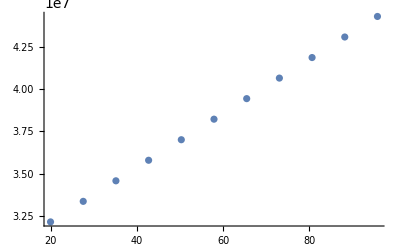

```mathematica
σxx1=-(MzL[0]*height/2)/Izz;
MzL[0];
σxx2=(MyL[0]*-width/2)/Iyy; 
σxx=σxx1+σxx2;


num=(95.8-20)/10;
uvec={};Do[AppendTo[uvec,Abs[σxx]],{Leng,20,95.8,num}]
data=Transpose@{Range[20,95.8,num],uvec};
ListPlot[data]
```

```mathematica
maxLeng=Solve[T*(Leng+Rfuse)== 5390000/FS,Leng];
maxLeng=Leng/.maxLeng[[1]]
```

42.0573

## Case 3 (Static)

```mathematica
ClearAll["Global`*"]
```

```mathematica
gfactor=1;
grav=32.2*gfactor; (*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=117.84;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
width=.65*ctip;(*box breadth (ft)*)
height=0.05443575 ctip;(*box height (ft)*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=.105*Lw; (*landing gear location (ft)*)
S=width*Lw; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=.1*12^3; (*density of aluminum (lb/ft3)*)
Wspar=ρAl*Lw*width*height;(*weight of spar (lbs)*)
e = 0.862; (* oswald effieciency factor*)

Izz=1/12 width *height^3; (*moment of inertia of lift(ft4)*)
Iyy=1/12 Lw*height^3; (*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=10.2*10^6*12^2; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS; 
(*yield stress of wing (lb/ft2)*)
Rfuse = 10.02; (*radius of fuselage (ft)*)
```

```mathematica
a=17.58; b=22.85; c=53.27; d=74.63;
 e=93.18; f=118.32; g=144.42; h=156.11;
(*pc=591.45; pf=2511.5; pp=321.41; OEW=289441.93; Wfuelun=83051.38;
 Wcheck=-pc*(35.69)-pc*(g-(c+croot))-pp*(146.62)-pf*(c+croot-c)-(OEW-Wfuelun)-244494*.3*2
Solve[0== -pc*(35.69)*((c-a)/2)-c*(g-(c+croot))*((g-(c+croot))/2+c+croot-a)-pp*(146.62)*((h-a)/2)-pf*(c+croot-c)*((croot)/2+c-a)-2*244494*.3*(c+croot/2-a)-(OEW-Wfuelun)*67+2*Flg*(e-a),Flg] (*Solving for Flg*)
sol3a=Solve[0== -Wto*(67)+2*Flg*(e-a),Flg];
Flg=Flg/.sol3a[[1]];*)
Solve[-67*Wto + 2Flg*(e-a) ==0,Flg]
Flg = 243717;
```

{{Flg→243717.}}

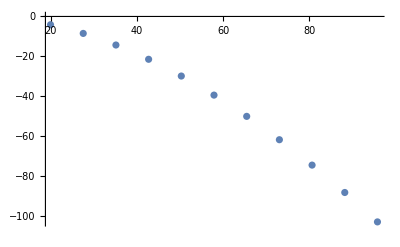

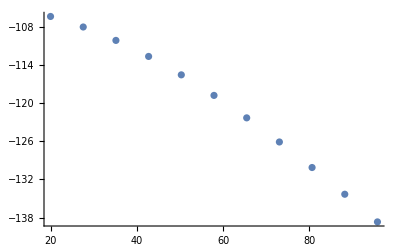

```mathematica
(* distributed load *)
py[x_]=0;
Integrate[py[x],{x,0,Lw}]; (*total lift*)

VyL[x_]=Integrate[-(py[x]-Wfuel/Llg-Wspar/Lw),x]+c1a;
VyM[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c2a;
VyR[x_]=Integrate[-(py[x]-Wspar/Lw),x]+c3a;

MzL[x_]=Integrate[-VyL[x],x]+c4a;
MzM[x_]=Integrate[-VyM[x],x]+c5a;
MzR[x_]=Integrate[-VyR[x],x]+c6a;

rotyL[x_]=Integrate[MzL[x]/(EE Izz),x]+c7a;
rotyM[x_]=Integrate[MzM[x]/(EE Izz),x]+c8a;
rotyR[x_]=Integrate[MzR[x]/(EE Izz),x]+c9a;

uyL[x_]=Integrate[rotyL[x],x]+c10a;
uyM[x_]=Integrate[rotyM[x],x]+c11a;
uyR[x_]=Integrate[rotyR[x],x]+c12a;

(*boundary and matching conditions*)
eq4a=VyR[Lw]==0;
eq5a=MzR[Lw]==0;
eq6a=uyL[0]==0;
eq7a=rotyL[0]==0;
eq8a=rotyL[Llg]==rotyM[Llg];
eq9a=rotyM[Leng]==rotyR[Leng];
eq10a=uyL[Llg]==uyM[Llg];
eq11a=uyM[Leng]==uyR[Leng];
eq12a=MzL[Llg]==MzM[Llg];
eq13a=MzM[Leng]==MzR[Leng];
eq14a=VyL[Llg]-Flg==VyM[Llg];
eq15a=VyM[Leng]+Weng==VyR[Leng];

sol2a=Solve[{eq4a,eq5a,eq6a,eq7a,eq8a,eq9a,eq10a,eq11a,eq12a,eq13a,eq14a,eq15a},{c1a,c2a,c3a,c4a,c5a,c6a,c7a,c8a,c9a,c10a,c11a,c12a}];
c1a=c1a/.sol2a[[1]];
c2a=c2a/.sol2a[[1]];
c3a=c3a/.sol2a[[1]];
c4a=c4a/.sol2a[[1]];
c5a=c5a/.sol2a[[1]];
c6a=c6a/.sol2a[[1]];
c7a=c7a/.sol2a[[1]];
c8a=c8a/.sol2a[[1]];
c9a=c9a/.sol2a[[1]];
c10a=c10a/.sol2a[[1]];
c11a=c11a/.sol2a[[1]];
c12a=c12a/.sol2a[[1]];

VyL[x_]=VyL[x];
VyM[x_]=VyM[x];
VyR[x_]=VyR[x];
MzL[x_]=MzL[x];
MzM[x_]=MzM[x];
MzR[x_]=MzR[x];
rotyL[x_]=rotyL[x];
rotyM[x_]=rotyM[x];
rotyR[x_]=rotyR[x];
uyL[x_]=uyL[x];
uyM[x_]=uyM[x];
uyR[x_]=uyR[x];

num=(95.8-20)/10;
uvec={};Do[AppendTo[uvec,uyR[Leng]],{Leng,20,95.8,num}]
data1=Transpose@{Range[20,95.8,num],uvec};
ListPlot[data1] (*deflection at Leng*)

uvec2={};Do[AppendTo[uvec2,uyR[Lw]],{Leng,20,95.8,num}]
data2=Transpose@{Range[20,95.8,num],uvec2};
ListPlot[data2] (*deflection at Lw*)
```

```mathematica
Leng = 30;
σxx1=-(MzL[0]*height/2)/Izz/144

num=(95.8-20)/10;
uvec3={};Do[AppendTo[uvec3,Abs[σxx]],{Leng,20,95.8,num}]
data=Transpose@{Range[20,95.8,num],uvec3};
ListPlot[data]
```

40381.5

-Graphics-